```mathematica
centralIdealData=<<"C:\\Users\\admin\\Documents\\Dropbox\\Grad School\\ActiveResearch\\static-exp-data\\Variance_1_Data\\CentralIdealExpLog_ExpVariance_1.txt";
```

```mathematica
centralNoisyData=<<"C:\\Users\\admin\\Documents\\Dropbox\\Grad School\\ActiveResearch\\static-exp-data\\Variance_1_Data\\CentralNoisyExpLog_ExpVariance_1.txt";
```

```mathematica
distrNoisyData=<<"C:\\Users\\admin\\Documents\\Dropbox\\Grad School\\ActiveResearch\\static-exp-data\\Variance_1_Data\\DistrNoisyExpLog_ExpVariance_1.txt";
```

```mathematica
CIAvgs=Mean[centralIdealData⟦2;;101⟧];
CISDevs=StandardDeviation[centralIdealData⟦2;;101⟧];
```

```mathematica
CNAvgs=Mean[centralNoisyData⟦2;;101⟧];
CNSDevs=StandardDeviation[centralNoisyData⟦2;;101⟧];
```

```mathematica
DNAvgs=Mean[distrNoisyData⟦2;;101⟧];
DNSDevs=StandardDeviation[distrNoisyData⟦2;;101⟧];
```

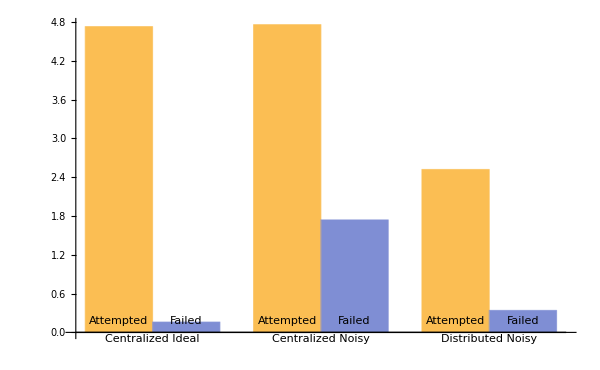

```mathematica
BarChart[{CIAvgs⟦3;;4⟧,CNAvgs⟦3;;4⟧,DNAvgs⟦3;;4⟧},BarSpacing->{0,.5},ChartLabels->{{"Centralized Ideal","Centralized Noisy","Distributed Noisy"}, Placed[{"Attempted","Failed"},Bottom]},BaseStyle->FontSize->17,ImageSize-> {600,400}]
```

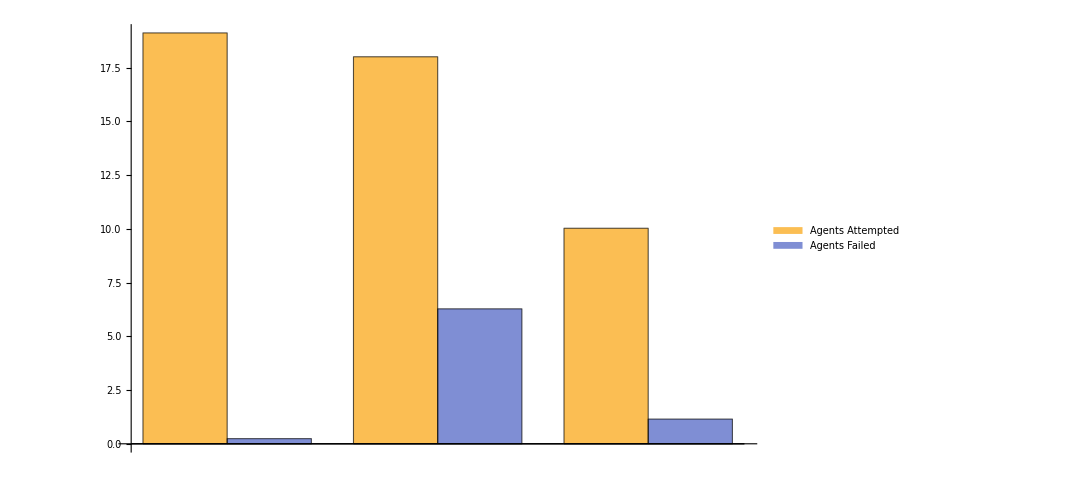

```mathematica
BarChart[{CIAvgs⟦5;;6⟧,CNAvgs⟦5;;6⟧,DNAvgs⟦5;;6⟧},BarSpacing->{0,.5},ChartLegends->Placed[{"Agents Attempted","Agents Failed"},Top],BaseStyle->FontSize->18,ImageSize-> {800,600}]
```